```mathematica
podatki=RandomVariate[NormalDistribution[0,1],2000];
```

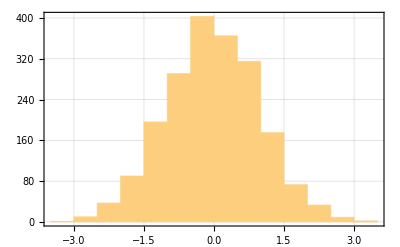

```mathematica
(* Dolocimo stevilo stolpcev *)
h1=Histogram[podatki,10,Frame->True,GridLines->Automatic,GridLinesStyle->Directive[Thin,Gray, Dashed]]
```

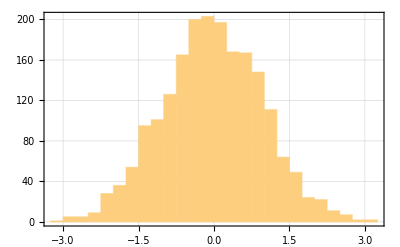

```mathematica
(* Dolocimo sirino stolpcev *)
h1=Histogram[podatki,{0.25},Frame->True,GridLines->Automatic,GridLinesStyle->Directive[Thin,Gray, Dashed]]
```

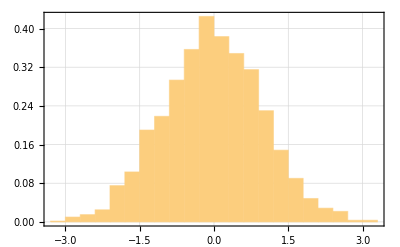

```mathematica
(* Verjetnostna porazdelitev podatkov *)
h1=Histogram[podatki,{0.3},"PDF",Frame->True,GridLines->Automatic,GridLinesStyle->Directive[Thin,Gray, Dashed]]
```

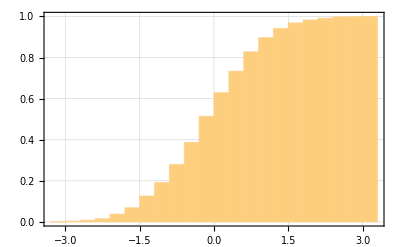

```mathematica
(* Kumulativna porazdelitev podatkov *)
h2=Histogram[podatki,{0.3},"CDF",Frame->True,GridLines->Automatic,GridLinesStyle->Directive[Thin,Gray, Dashed]]
```

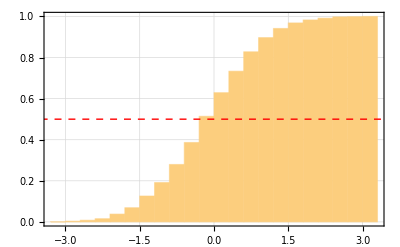

```mathematica
(* Crta cez histogram/graf *)
Show[h2,Graphics[{Dashed,Red,Line[{{-5,0.5},{5,0.5}}]}]]
```

```mathematica
(* Mera za meritve (normiramo z dolzino celotnega intervala) *)
sredina=Table[(e[[i+1]]-e[[i-1]])/2,{i,2,Length[e]-1}];
utezi=Join[{e[[1]]-e[[1]]},sredina,{e[[Length[e]]]-e[[Length[e]-1]]}]/(Max[e]-Min[e]);
```

```mathematica
Histogram[WeightedData[podatki,utezi]]
```